# iScat Image Recognition - v1

## by Karolis Misiunas

Usage:
Execute commands by selecting a cell and pressing Shift+Enter. Remmeber to execute the command aftr each edit!

## Step 0 - Load the program

```mathematica
Quit[];
```

```mathematica
Import[ NotebookDirectory[] <> "packages/VideoTracking.m"]
```

## Step 1 - Select the video file

```mathematica
SelectVideo[ "/Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/c111vid_0.avi"]
```

c111vid_0.avi has 20000 frames and is 200x200

## Step 2 - Select region of intrest

```mathematica
SelectROI[ROIFullImage[]]
```

(0 | 200
200 | 200
200 | 0
0 | 0)

```mathematica
{{102,98},{118,98},{118,91},{102,91}}
```

{{102,98},{118,98},{118,91},{102,91}}

## Step 3 - Compute the background image

```mathematica
UpdateBackgroung[1, NumberOfFrames[]]
```

-Graphics-

```mathematica
SmartMeanBackground[ Range[1,400] ]
```

-Graphics-

```mathematica
MeanBackground[ Range[1,400] ]
```

-Graphics-

```mathematica
ImageDifference[Out@5, Out@3] // ImageAdjust
```

-Graphics-

```mathematica
GetFrame[17001]
```

-Graphics-

```mathematica
VideoIO`Private`bufferVideoTimeStamp
```

{0,0,0,0,0,0,0,0,0,0,0,3.605427659393681×10^9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.605427629856951×10^9,3.605427641545106×10^9,0,0,0,0,0,0,0,0,0,0,3.605427670232169×10^9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
VideoIO`Private`BufferMemorySize[]
```

64.7936

```mathematica
SetOptions[VideoIO, BufferSizeMB -> 55]
```

{BufferSizeMB→55,BufferBlockSize→400}

```mathematica
Length[{}]
```

0

## Step 4 - configure tracing algorithm

```mathematica
VideoTracking`SubstractBG[img_] := ImageDifference[ img, CurrentBackground[] ];

Options[VideoTracking];

SetOptions[VideoTracking, 
FilterCircularity->{0.5,1.4},
FilterArea-> {4,50},
UpdateBackgroung->True,
Threshold -> 0.04
]
```

{Threshold→0.04,FilterArea→{4,50},FilterCircularity→{0.5,1.4},AnalysisBlockSize→4000,UpdateBackgroung→True}

## Step 5 - Inspect per frame basis (run many times!)

{{13.9605,4.15157}}

-Graphics-

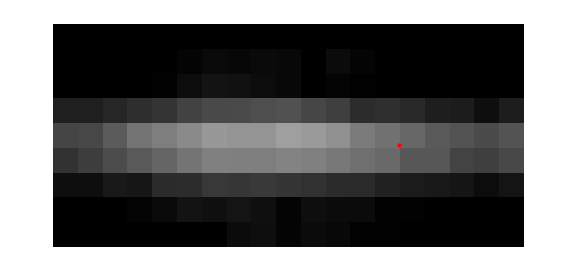

-Graphics-

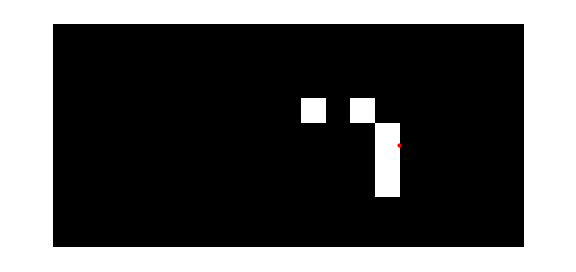

Area→{1→1.,2→4.75}

Circularity→{1→0.886227,2→0.590818}

```mathematica
frame =9623;

ShowTrackOverlayed[img_,list_]:=Show[img,Graphics@Flatten@{Red,Point[#]&/@list},ImageSize->Large]

curPos = AnalyseFrame[frame]
ShowTrackOverlayed[ GetFrame[frame] , curPos]
ShowTrackOverlayed[ CurrentBackground[], curPos]
ShowTrackOverlayed[ SubstractBG@GetFrame[frame] , curPos] //ImageAdjust
ShowTrackOverlayed[ FrameBinarize@SubstractBG@GetFrame[frame] , curPos]

"Area"-> ComponentMeasurements[ FrameBinarize@SubstractBG@GetFrame[frame] ,"Area"]

"Circularity"-> ComponentMeasurements[ FrameBinarize@SubstractBG@GetFrame[frame] ,"Circularity"]
```

```mathematica
Show[ GetFrames[7148][[1]], ImageSize-> Large]
```

-Graphics-

## Step 6 - Analyse video in Lumps

```mathematica
outputFolder = "H:\\Karolis\\Jerome\\experiment N4\\channel 4\\N4vid_4302250\\";

from = 1;
to = NumberOfFrames[];


out = RunAnalysis[ from , to ] // AbsoluteTiming;

Print["Computation took "<>ToString@out[[1]] <> " sec"];

Export[ 
outputFolder<>FileBaseName[ VideoFile[] ]<>".csv",  
out[[2]] 
];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

$Aborted

Computation took 8857.407000 sec

## Step 7 - Run step 6 again with increased value

## Other stuff

```mathematica
"video time" -> NumberOfFrames[] /30 // N
```

video time→52.7667

```mathematica
out
```

{}

```mathematica
try = FrameBinarize @SubstractBG @ GetFrame[1]

ComponentMeasurements[try , "Circularity" ]
```

-Graphics-

{1→0.734227,2→0.781579}

## One step computation

```mathematica
ComputeVideo[file_] := Module[{},
oldROI = CurrentROI[] ;

folder = DirectoryName[file];
Print @ SelectVideo[  file];

Print["video is "<> ToString@(NumberOfFrames[] /30 // N) <> " sec long"];

Print @ SelectROI[ oldROI ];

Print @ UpdateBackgroung[1, NumberOfFrames[] ] ;

outputFolder = folder<>"tracks\\";

out = RunAnalysis[1, NumberOfFrames[]] // AbsoluteTiming;

Print["Computation took "<> ToString@out[[1]] <> " sec"];

Print @ Export[ 
outputFolder<>FileBaseName[file] <>".csv",  
out[[2]] 
];

]
```

video 21 - had fit problem - investigate!
video 22 - bg not computed correctlly!
video 26,27 - background cound not be computed
35 - bg imperfect
58 - one of the last fits was low accuracy

## Automatic analysis of many videos

Jerome, run step 0, step 1,2,4 and 5 on demand. Then initialise “One step computation” and prepare comands below:

```mathematica
analyseTheseFiles = {"file1" , "file2", "file3"};

Do[ ComputeVideo[f], {f, analyseTheseFiles }]
```

Good luck!

## Determine optimal video buffer size

See how loading speed depends on the number of frames

```mathematica
SelectVideo["H:\\Karolis\\Experiments\\03_March\\06\\long video.avi"]
```

long video.avi has 140270 frames and is 720x480

```mathematica
LoadNFrames[n_] := (GetFrames[Range[1000,1000+n]]; n);

times = Table[ AbsoluteTiming[  LoadNFrames[n] ], {n, 1,1001, 100}]
```

(0.18118 | 1
0.46263 | 101
0.80236 | 201
1.17954 | 301
1.59445 | 401
2.08608 | 501
2.6675 | 601
3.75396 | 701
3.83519 | 801
4.42855 | 901
5.38113 | 1001)

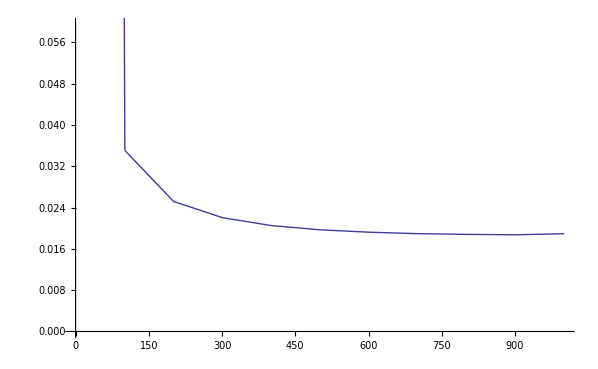

```mathematica
timesPerFrame = Transpose@ {times[[;;,2]] ,  times [[;;,1]]/times [[;;,2]] };
ListPlot[timesPerFrame, Joined-> True, AxesOrigin->{0,0}]
```

```mathematica
0.0156
```

```mathematica
Table[ n, {n, 1,2000, 200}]
```

{1,201,401,601,801,1001,1201,1401,1601,1801}

```mathematica
Range[10,20]
```

{10,11,12,13,14,15,16,17,18,19,20}

### ⇒ Should load in lums of at least 100 frames and smaller than 500 frames for videos with 3000 frames.

### ⇒ In big videos (>140k fr) It seems to be beneficial to load longer bits: from 400 to 1000.